## Methods

```mathematica
headerList={"Pascals(in/Hg)","Altitude(ft)","Temperature(*C)","Time(s)"};
```

```mathematica
GetData[fileName0_]:=
Module[{file = fileName0,v},
v=Import[file];
v=StringSplit[v,"\t"];
v=StringSplit[v,"\n"];
v
]
```

```mathematica
CleanDataRecord[record0_]:=
Module[{record = record0,test},
test = StringSplit[#,","]&/@record;
test =Drop[test,1];
test=ToExpression/@test;
test=PrependTo[test,headerList];
test=Dataset[Map[AssociationThread[First[test],#]&,Rest[test]]];
test
]
```

```mathematica
DisplayData[dataList0_]:=
Module[{l=dataList0,gg,a,b,c,d,labels,shortLabels,vals},
row[text_,plot_]:=Row[{text,plot},Alignment->Center];
labels=Text[Style[#,18]]&/@{"Pascals(in/Hg)","Altitude(ft)","Temperature(*C)","Time(s)"};
shortLabels = Text[Style[#,18]]&/@{"Altitude(ft)","dA/dt","Temperature(*C)"};
(*a=ListLinePlot[l[[All,1]],ImagePadding->{{50,50},{10,10}},ImageSize->Medium,AspectRatio->1/GoldenRatio];*)
b=ListLinePlot[l[[All,2]],ImagePadding->{{50,50},{10,10}},ImageSize->Large,AspectRatio->1/GoldenRatio];
c=ListLinePlot[l[[All,3]],ImagePadding->{{50,50},{10,10}},ImageSize->Large,AspectRatio->1/GoldenRatio];
vals=RateOfChange[l[[All,2]]];
d=ListPlot[vals,ImagePadding->{{50,50},{10,10}},ImageSize->Large,AspectRatio->1/GoldenRatio];
gg2=GraphicsGrid[Partition[row@@@Thread[{shortLabels,{b,d,c}}],3],Spacings->{10,20},Frame->None,ImageSize->Full];
gg2
]
```

```mathematica
RateOfChange[list0_]:=
Module[{list = list0,temp,result},
temp = list;
result={};
While[Length[temp]>1,
result=AppendTo[result,temp[[1]]-temp[[2]]];
temp=Drop[temp,1];
];
result
]
```

## Execute

{Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>]}

8

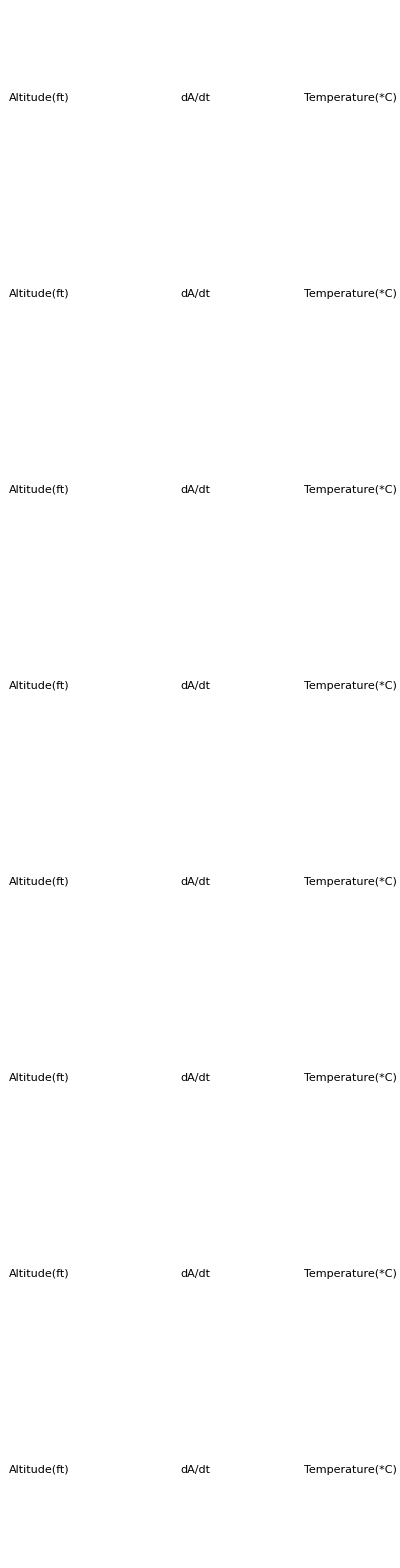

```mathematica
SetDirectory[NotebookDirectory[]];
data=GetData["RC.TXT"];
cleanData=CleanDataRecord/@data
cleanData//Length
graphs=DisplayData/@cleanData;
graphs//TableForm
```

```mathematica
cleanData[[1]]//Normal
```

{<|Pascals(in/Hg)→28.26,Altitude(ft)→1647.38,Temperature(*C)→23.69,Time(s)→0|>,<|Pascals(in/Hg)→28.26,Altitude(ft)→1646.15,Temperature(*C)→23.75,Time(s)→1|>,<|Pascals(in/Hg)→28.26,Altitude(ft)→1644.71,Temperature(*C)→23.69,Time(s)→2|>,<|Pascals(in/Hg)→28.26,Altitude(ft)→1642.66,Temperature(*C)→23.75,Time(s)→3|>,<|Pascals(in/Hg)→28.26,Altitude(ft)→1644.1,Temperature(*C)→23.75,Time(s)→4|>,<|Pascals(in/Hg)→28.26,Altitude(ft)→1645.12,Temperature(*C)→23.75,Time(s)→5|>,<|Pascals(in/Hg)→28.26,Altitude(ft)→1645.33,Temperature(*C)→23.75,Time(s)→5|>,<|Pascals(in/Hg)→28.26,Altitude(ft)→1644.71,Temperature(*C)→23.75,Time(s)→6|>,<|Pascals(in/Hg)→28.26,Altitude(ft)→1645.53,Temperature(*C)→23.75,Time(s)→7|>,<|Pascals(in/Hg)→28.26,Altitude(ft)→1645.12,Temperature(*C)→23.75,Time(s)→8|>,<|Pascals(in/Hg)→28.26,Altitude(ft)→1643.28,Temperature(*C)→23.75,Time(s)→9|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1641.84,Temperature(*C)→23.69,Time(s)→10|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1641.02,Temperature(*C)→23.75,Time(s)→10|>,<|Pascals(in/Hg)→28.26,Altitude(ft)→1642.46,Temperature(*C)→23.69,Time(s)→11|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.41,Temperature(*C)→23.69,Time(s)→12|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.56,Temperature(*C)→23.69,Time(s)→13|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1636.51,Temperature(*C)→23.69,Time(s)→14|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.97,Temperature(*C)→23.62,Time(s)→15|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.95,Temperature(*C)→23.62,Time(s)→15|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.36,Temperature(*C)→23.62,Time(s)→16|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1641.64,Temperature(*C)→23.56,Time(s)→17|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.2,Temperature(*C)→23.56,Time(s)→18|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1639.18,Temperature(*C)→23.56,Time(s)→19|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.41,Temperature(*C)→23.5,Time(s)→20|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.2,Temperature(*C)→23.5,Time(s)→20|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.,Temperature(*C)→23.5,Time(s)→21|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.,Temperature(*C)→23.5,Time(s)→22|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.77,Temperature(*C)→23.5,Time(s)→23|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.97,Temperature(*C)→23.5,Time(s)→24|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.36,Temperature(*C)→23.5,Time(s)→24|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.56,Temperature(*C)→23.44,Time(s)→25|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.56,Temperature(*C)→23.44,Time(s)→26|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.95,Temperature(*C)→23.44,Time(s)→27|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.56,Temperature(*C)→23.44,Time(s)→28|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1639.59,Temperature(*C)→23.44,Time(s)→29|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.97,Temperature(*C)→23.38,Time(s)→29|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.41,Temperature(*C)→23.38,Time(s)→30|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1639.38,Temperature(*C)→23.38,Time(s)→31|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1639.59,Temperature(*C)→23.31,Time(s)→32|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.,Temperature(*C)→23.31,Time(s)→33|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.97,Temperature(*C)→23.31,Time(s)→34|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.62,Temperature(*C)→23.25,Time(s)→34|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1642.66,Temperature(*C)→23.25,Time(s)→35|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.74,Temperature(*C)→23.25,Time(s)→36|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.41,Temperature(*C)→23.25,Time(s)→37|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.56,Temperature(*C)→23.25,Time(s)→38|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.97,Temperature(*C)→23.25,Time(s)→39|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.33,Temperature(*C)→23.25,Time(s)→39|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.13,Temperature(*C)→23.25,Time(s)→40|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.97,Temperature(*C)→23.19,Time(s)→41|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.56,Temperature(*C)→23.12,Time(s)→42|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1639.59,Temperature(*C)→23.12,Time(s)→43|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.77,Temperature(*C)→23.12,Time(s)→43|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.95,Temperature(*C)→23.12,Time(s)→44|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.97,Temperature(*C)→23.06,Time(s)→45|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1639.79,Temperature(*C)→23.06,Time(s)→46|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.,Temperature(*C)→23.,Time(s)→47|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.62,Temperature(*C)→23.,Time(s)→48|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.62,Temperature(*C)→23.,Time(s)→48|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1641.02,Temperature(*C)→22.94,Time(s)→49|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1641.64,Temperature(*C)→22.94,Time(s)→50|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1639.38,Temperature(*C)→22.94,Time(s)→51|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.2,Temperature(*C)→22.94,Time(s)→52|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1639.18,Temperature(*C)→22.94,Time(s)→53|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1641.02,Temperature(*C)→22.94,Time(s)→53|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.62,Temperature(*C)→22.94,Time(s)→54|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.62,Temperature(*C)→22.94,Time(s)→55|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.62,Temperature(*C)→22.94,Time(s)→56|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1642.46,Temperature(*C)→22.88,Time(s)→57|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1641.23,Temperature(*C)→22.88,Time(s)→58|>,<|Pascals(in/Hg)→28.26,Altitude(ft)→1642.46,Temperature(*C)→22.88,Time(s)→58|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1642.25,Temperature(*C)→22.88,Time(s)→59|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1639.59,Temperature(*C)→22.94,Time(s)→60|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1639.79,Temperature(*C)→22.88,Time(s)→61|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1641.64,Temperature(*C)→22.88,Time(s)→62|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1642.46,Temperature(*C)→22.75,Time(s)→63|>,<|Pascals(in/Hg)→28.26,Altitude(ft)→1642.25,Temperature(*C)→22.69,Time(s)→63|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1641.64,Temperature(*C)→22.69,Time(s)→64|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.56,Temperature(*C)→22.62,Time(s)→65|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1639.18,Temperature(*C)→22.56,Time(s)→66|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1641.64,Temperature(*C)→22.56,Time(s)→67|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1641.02,Temperature(*C)→22.56,Time(s)→68|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1644.1,Temperature(*C)→22.5,Time(s)→68|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1641.23,Temperature(*C)→22.5,Time(s)→69|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.62,Temperature(*C)→22.5,Time(s)→70|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.2,Temperature(*C)→22.5,Time(s)→71|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.,Temperature(*C)→22.44,Time(s)→72|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.41,Temperature(*C)→22.44,Time(s)→73|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.2,Temperature(*C)→22.38,Time(s)→73|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.62,Temperature(*C)→22.38,Time(s)→74|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.82,Temperature(*C)→22.31,Time(s)→75|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1639.59,Temperature(*C)→22.25,Time(s)→76|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.13,Temperature(*C)→22.25,Time(s)→77|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.33,Temperature(*C)→22.12,Time(s)→77|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1635.9,Temperature(*C)→22.06,Time(s)→78|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1636.92,Temperature(*C)→22.,Time(s)→79|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.97,Temperature(*C)→22.,Time(s)→80|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.15,Temperature(*C)→21.94,Time(s)→81|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.95,Temperature(*C)→21.94,Time(s)→82|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.13,Temperature(*C)→21.94,Time(s)→82|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.95,Temperature(*C)→21.94,Time(s)→83|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.97,Temperature(*C)→21.88,Time(s)→84|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1636.51,Temperature(*C)→21.94,Time(s)→85|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1641.43,Temperature(*C)→21.88,Time(s)→86|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.2,Temperature(*C)→21.88,Time(s)→87|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.95,Temperature(*C)→21.88,Time(s)→87|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.97,Temperature(*C)→21.88,Time(s)→88|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.13,Temperature(*C)→21.88,Time(s)→89|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.2,Temperature(*C)→21.81,Time(s)→90|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.97,Temperature(*C)→21.81,Time(s)→91|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.,Temperature(*C)→21.75,Time(s)→92|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.2,Temperature(*C)→21.69,Time(s)→92|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.2,Temperature(*C)→21.69,Time(s)→93|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.77,Temperature(*C)→21.69,Time(s)→94|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.,Temperature(*C)→21.62,Time(s)→95|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.,Temperature(*C)→21.62,Time(s)→96|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.2,Temperature(*C)→21.56,Time(s)→97|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1638.56,Temperature(*C)→21.56,Time(s)→97|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.95,Temperature(*C)→21.56,Time(s)→98|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.54,Temperature(*C)→21.56,Time(s)→99|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1640.2,Temperature(*C)→21.56,Time(s)→100|>,<|Pascals(in/Hg)→28.27,Altitude(ft)→1637.13,Temperature(*C)→21.56,Time(s)→101|>}